```mathematica
SetDirectory[NotebookDirectory[]];
PrintTemporary["importing files"];
d = Import@FileNames["magnetpendel.dat"][[1]];
PrintTemporary["deleting emptys"];
d=DeleteCases[d,{}];

PrintTemporary["plotting"];
Show[
ListDensityPlot[
d[[All,1;;3]],
ColorFunction->(Blend[{Red,Green,Blue},#]&),
PlotTheme->"pub"
],(*
ListDensityPlot[
d[[All,{1,2,4}]],
ColorFunction->(RGBColor[0,0,0,#]&),
PlotLegends->Automatic,
PlotRange->{0,Automatic},
PlotTheme->"pub",
ColorFunctionScaling->True
],*)
Graphics[{
White,AbsolutePointSize[5],
Point@Import@FileNames["Magnete.dat"][[1]]
}]
]
Export["img/plot.pdf",%,ImageResolution->600,"AllowRasterization"->True];
```

-Graphics-

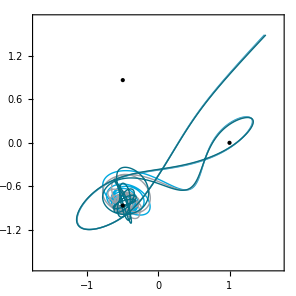

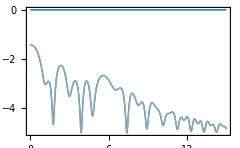

```mathematica
SetDirectory[NotebookDirectory[]];
d = Import@FileNames["path.dat"][[1]];
d=SplitBy[d,#1=={}&];
d = DeleteCases[d,{{}}];

ListLinePlot[
Evaluate@d[[All,1;;15000,{2,3}]],
PlotTheme->"pub",
PlotRange->{{-1.7,1.7},{-1.7,1.7}},
Axes->False,
Epilog->{
AbsolutePointSize[3],
Point@Import@FileNames["Magnete.dat"][[1]]
},
AspectRatio->Automatic
]
Export["img/xy.pdf",%];

ListLinePlot[
{d[[1,1;;15000,{1,4}]],d[[1,1;;15000,{1,5}]],d[[1,1;;15000,{1,6}]]},
PlotTheme->"pub",
PlotLegends->{"ges","mag","kin + schwerkraft"}
]
```